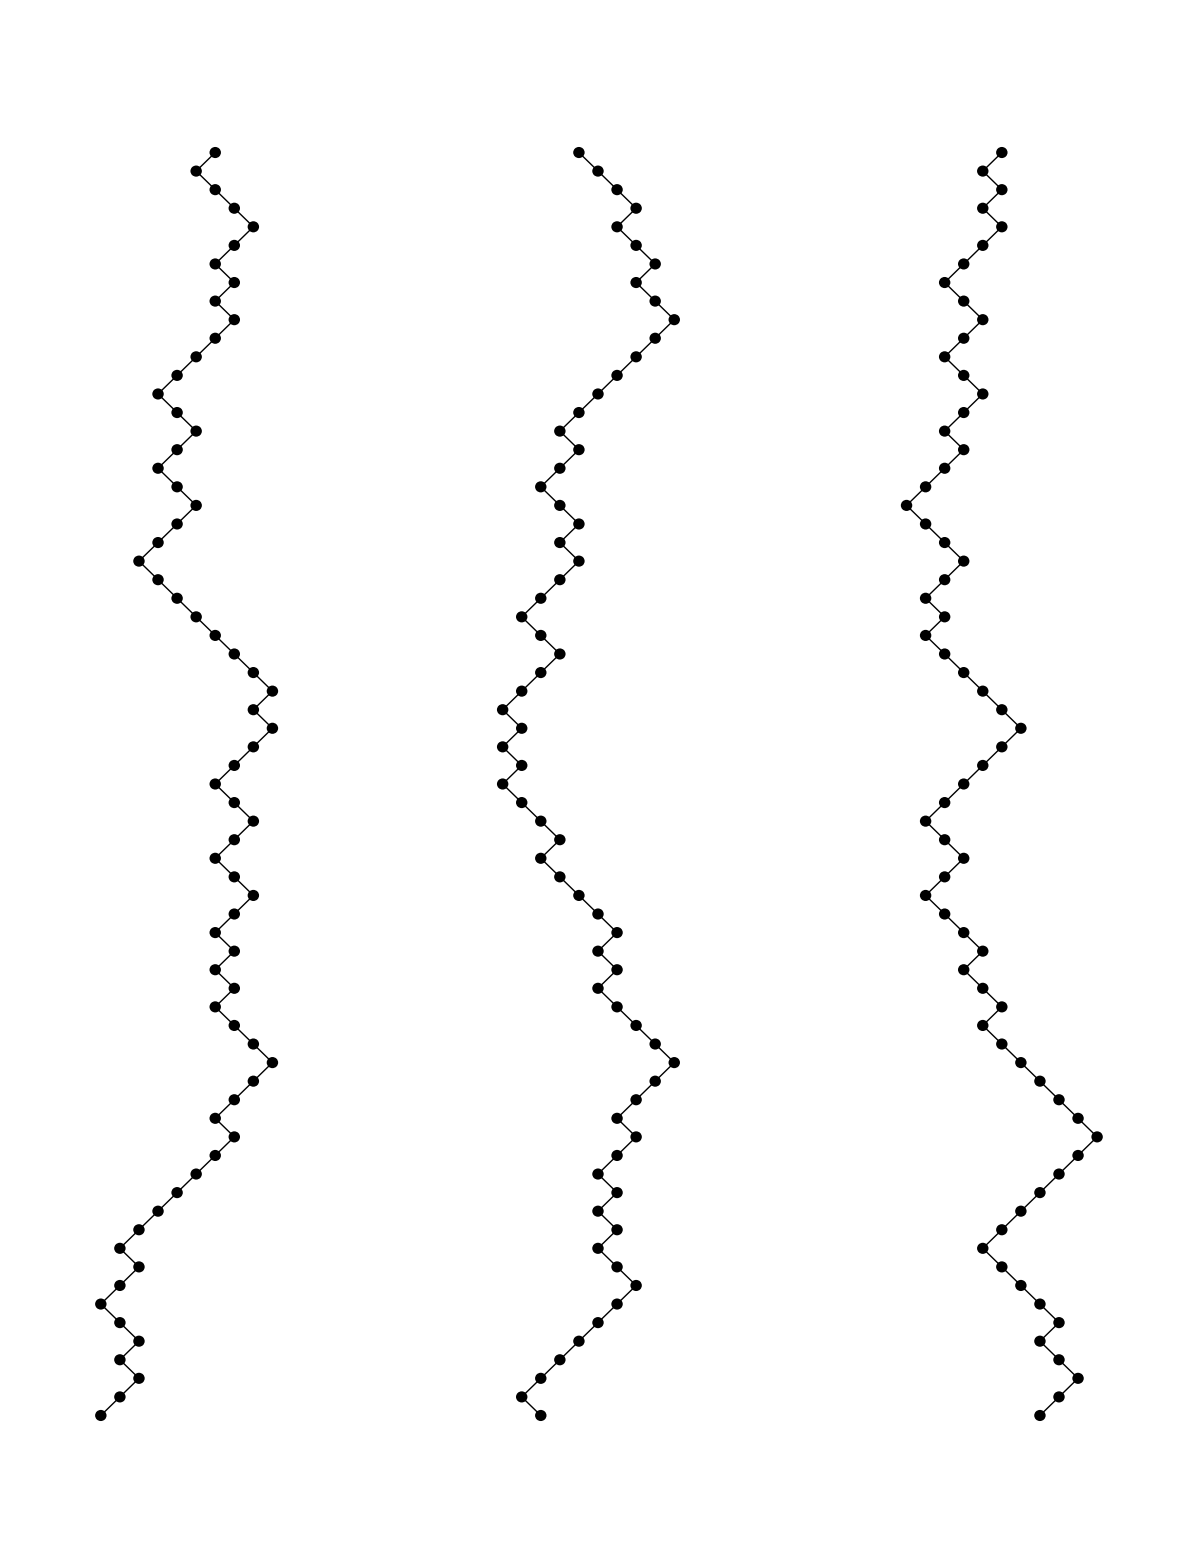

```mathematica
SeedRandom[3536,Method->"Rule30CA"];
GraphicsRow[Table[Graphics[{{(Disk[#,0.3]&)/@#,Line[#]}&[Transpose[{#,-Range[Length[#]]}]]},]&@FoldList[Plus,0,RandomChoice[{1,-1},68]],3]]
```